```mathematica
(* Trying to make shells with the Lorentz-Lorenz Equation *)

(* Declare constants *)
Clear["Global`*"];
startTime = DateString[];

NAvagadro=6.022*10^23;  (* Avagadro's number *)
R=8.3145; (*J/mol K; universal gas constant*)
k = 1.3806488 ; (* m^2 kgs^-2 K^-1; Boltzmann constant *)
G = 6.67*10^-11; (* universal gravitational constant in mks units *)

αN2=1.71*10^-30;  (* m^3, mean polarizability of Subscript[N, 2] gas *)
μN2=0.028; (* kg; molar mass of Subscript[N, 2] *)


Subscript[α, air]=2.133*10^-29;

p0 = 0.3; (* N/m^2; assumed surface pressure of Pluto *)
T = 50; (* K; assumed atmospheric temperature for isothermal model *)
MPluto = 1.29*10^22; (* kg; mass of Pluto *)
rSurf = 11950000; (* m; assumed surface radius of Pluto *)
```

```mathematica
(* local gravity as a function of r *)
Gravity[r_]:=G*MPluto/r^2;

(* pressure as a function of height *)
Pressure[p0_,M_,h_,T_]:=p0 E^((-M Gravity[h+rSurf] h)/(k T));

(* Snell's Law function that gives the new light path angle (Subscript[θ, out]) given an entrance angle and refractivities of the two media; remember that the θ values here are relative to the normal, not to the horizontal *)
(* TODO - might need a negative here because of the way Snell's law defines the angles *)
SnellsLaw[θin_,nin_,nout_]:=ArcSin[Sin[θin]nin/nout];

(* Lorentz-Lorenz Equation for n values close to 1: returns a refractive index n *)
LorentzLorenz[α_,p_,T_]:=√(1+(4π NAvagadro α p)/(R T));
```

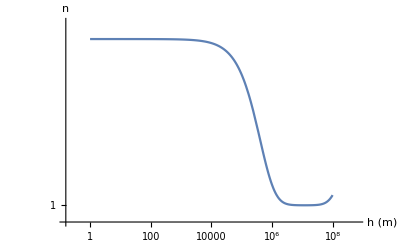

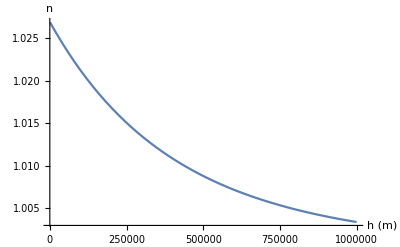

```mathematica
minHeight = 1;
maxHeight = 100000000; (* 1000 km *)

(* pressure plot *)
Plot[Pressure[p0,μN2,h,T],{h,minHeight,maxHeight},AxesLabel->{"radial distance","pressure"}];

(* plot of refractive index n *)
LogLogPlot[LorentzLorenz[αN2,Pressure[p0,μN2,h,T],T],{h,minHeight,maxHeight},AxesLabel->{"h (m)","n"}]
Plot[LorentzLorenz[10^-23,Pressure[p0,μN2,h,T],T],{h,1000.,1000000},AxesLabel->{"h (m)","n"}]
ListPlot[Table[LorentzLorenz[10^-23,Pressure[p0,0.28,h,T],T],{h,1000,100000}]];

(* with these plots, gravity is getting weaker faster than the height is increasing, causing the kink *)
```